# κτS^2 Secondary structure prediction by the use of the curvature and torsions of the geometrical curve of the protein backbone

## Initialization of the program

```mathematica
αβγscoring=Import[ToString[NotebookDirectory[]<>"probability_hsc_prot_186.dat"],"Table"];
```

```mathematica
dataα=Table[{αβγscoring⟦i,1;;2⟧,αβγscoring⟦i,3⟧},{i,Length[αβγscoring]}];
dataβ=Table[{αβγscoring⟦i,1;;2⟧,αβγscoring⟦i,4⟧},{i,Length[αβγscoring]}];
dataγ=Table[{αβγscoring⟦i,1;;2⟧,αβγscoring⟦i,5⟧},{i,Length[αβγscoring]}];
```

```mathematica
functionα=Interpolation[dataα];
functionβ=Interpolation[dataβ];
functionγ=Interpolation[dataγ];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

```mathematica
range1={{x,0.51,0.9899999999999978},{y,-3.041592653589793,3.158407346410199}};
```

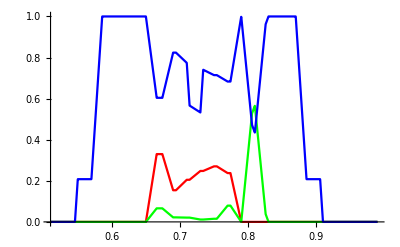

```mathematica
Plot[Evaluate[{functionα[x,3.],functionβ[x,3.],functionγ[x,3.]}],range1⟦1⟧,PlotStyle->{Red,Green,Blue}]
```

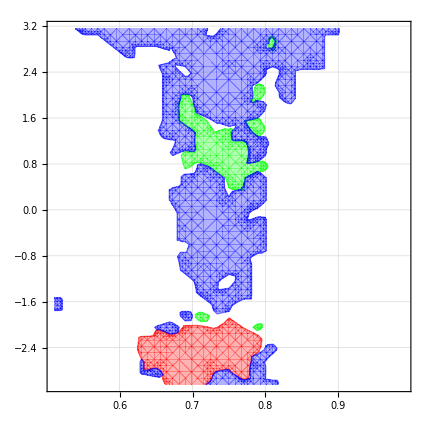

```mathematica
Show[
ContourPlot[functionα[x,y],range1⟦1⟧,range1⟦2⟧,PlotRange->{0,1.1},ContourShading->{None,{Opacity[0.3],Red}},ContourStyle->Red,Contours->{0.55}(*Table[y,{y,0.5,1,0.025}]*),GridLines->Automatic],
ContourPlot[functionβ[x,y],range1⟦1⟧,range1⟦2⟧,PlotRange->{0,1.1},ContourShading->{None,{Opacity[0.3],Green}},ContourStyle->Green,Contours->{0.5}(*Table[y,{y,0.5,1,0.025}]*)],
ContourPlot[functionγ[x,y],range1⟦1⟧,range1⟦2⟧,PlotRange->{0,1.1},ContourShading->{None,{Opacity[0.3],Blue}},ContourStyle->Blue,Contours->{0.45}(*Table[y,{y,0.5,1,0.025}]*)]
]
```

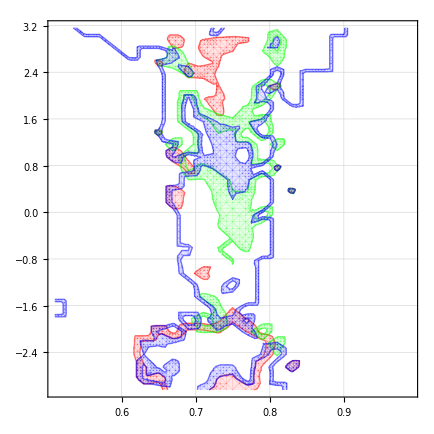

```mathematica
Show[
ContourPlot[functionα[x,y],range1⟦1⟧,range1⟦2⟧,PlotRange->{0,1.1},ContourShading->{None,{Opacity[0.1],Red}},ContourStyle->Red,Contours->{0.25,0.55}(*Table[y,{y,0.5,1,0.025}]*),GridLines->Automatic],
ContourPlot[functionβ[x,y],range1⟦1⟧,range1⟦2⟧,PlotRange->{0,1.1},ContourShading->{None,{Opacity[0.1],Green}},ContourStyle->Green,Contours->{0.25,0.5}(*Table[y,{y,0.5,1,0.025}]*)],
ContourPlot[functionγ[x,y],range1⟦1⟧,range1⟦2⟧,PlotRange->{0,1.1},ContourShading->{None,{Opacity[0.1],Blue}},ContourStyle->Blue,Contours->{0.25,0.45}(*Table[y,{y,0.5,1,0.025}]*)]
]
```

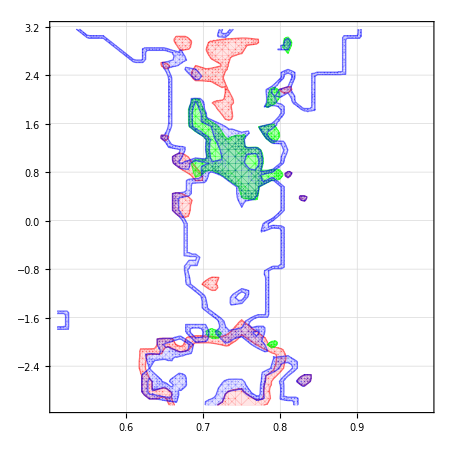

```mathematica
Show[
ContourPlot[functionα[x,y],range1⟦1⟧,range1⟦2⟧,PlotRange->{0,1},ContourShading->{None,{Opacity[0.1],Red}},ContourStyle->Red,Contours->{0.25,0.55}(*Table[y,{y,0.5,1,0.025}]*),GridLines->Automatic],
ContourPlot[functionβ[x,y],range1⟦1⟧,range1⟦2⟧,PlotRange->{0,1},ContourShading->{None,{Opacity[0.3],Green}},ContourStyle->Green,Contours->{0.5}(*Table[y,{y,0.5,1,0.025}]*)],
ContourPlot[functionγ[x,y],range1⟦1⟧,range1⟦2⟧,PlotRange->{0,1},ContourShading->{None,{Opacity[0.1],Blue}},ContourStyle->Blue,Contours->{0.25,0.45}(*Table[y,{y,0.5,1,0.025}]*)]
]
```

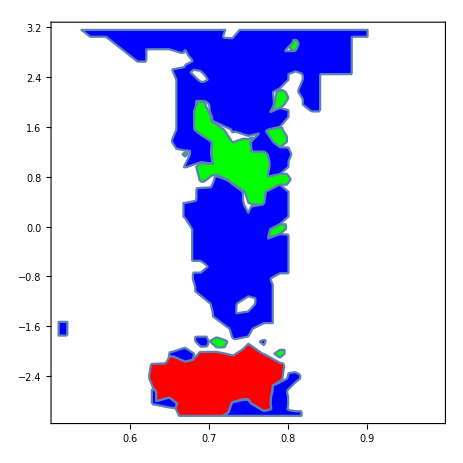

```mathematica
Show[RegionPlot[functionα[x,y]>0.55,range1⟦1⟧,range1⟦2⟧,PlotStyle->Red,PlotPoints->60],RegionPlot[functionβ[x,y]>0.5,range1⟦1⟧,range1⟦2⟧,PlotStyle->Green,PlotPoints->60],RegionPlot[functionγ[x,y]>0.45,range1⟦1⟧,range1⟦2⟧,PlotStyle->Blue,PlotPoints->60](*,RegionPlot[0.25<functionα[x,y]<0.55,range⟦1⟧,range⟦2⟧,PlotStyle->{Opacity[0.5],LightRed},PlotPoints->60],RegionPlot[0.25<functionβ[x,y]<0.5,range⟦1⟧,range⟦2⟧,PlotStyle->{Opacity[0.5],LightGreen},PlotPoints->60],RegionPlot[0.25<functionγ[x,y]<0.45,range⟦1⟧,range⟦2⟧,PlotStyle->{Opacity[0.5],LightBlue},PlotPoints->60]*)]
```

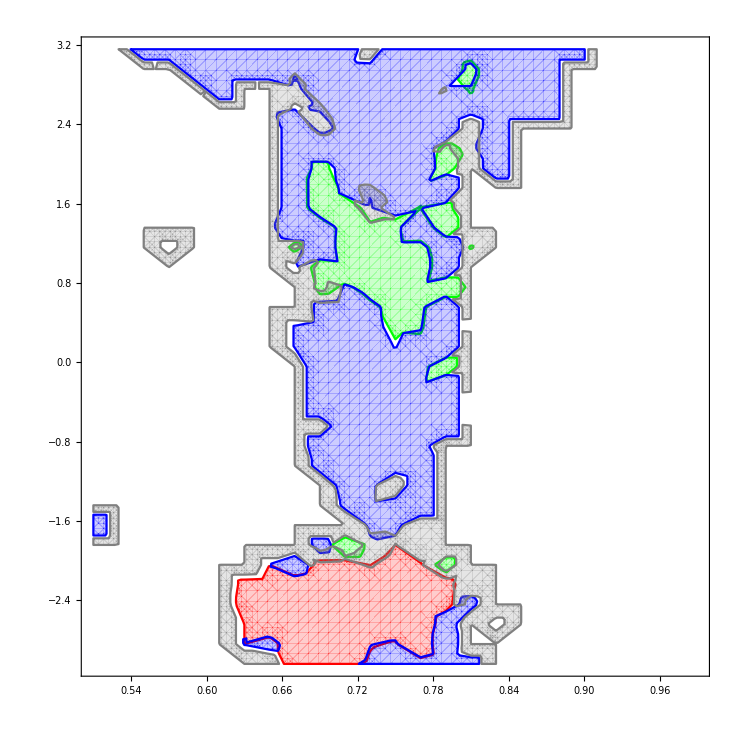

```mathematica
Show[RegionPlot[functionα[x,y]≥ 0.5,range1⟦1⟧,range1⟦2⟧, PlotStyle->{Opacity[0.2],Red},BoundaryStyle->Red,PlotPoints->60],
RegionPlot[functionβ[x,y]>0.45,range1⟦1⟧,range1⟦2⟧,PlotStyle->{Opacity[0.2],Green},BoundaryStyle->Green,PlotPoints->60],
RegionPlot[functionγ[x,y]>0.476,range1⟦1⟧,range1⟦2⟧,PlotStyle->{Opacity[0.2],Blue},BoundaryStyle->Blue,PlotPoints->60],RegionPlot[0.0<Max[{Abs[functionα[x,y]-functionβ[x,y]],Abs[functionα[x,y]-functionγ[x,y]],Abs[functionγ[x,y]-functionβ[x,y]]}]<0.333,range1⟦1⟧,range1⟦2⟧,PlotStyle->{Opacity[0.2],Gray},BoundaryStyle->Gray,PlotPoints->60]]
```